```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

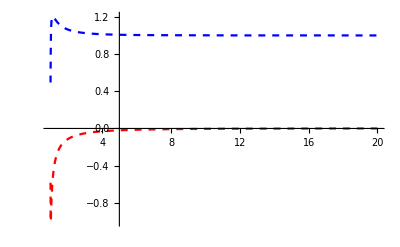

{AIn→0.79339+0.686002 ⅈ,AOut→-0.104521-0.298566 ⅈ}

0.916621

{0.0909639,0.909036}

```mathematica
Block[{ω,l,r∞,r0,R∞,Rp∞,ν,μ1,s,μ2},
ω=2/5;l=0;s=0;
r∞=20;r0=1+10^-8;
ν=0;μ1=0;μ2=-(s+1);
R∞=1;
Rp∞=0;
solIn=NDSolve[{R''[r]+((1-2I ω r^2)/(r(r-1)))R'[r]-((l(l+1)+1/r)/(r(r-1)))R[r]==0,R[r∞]==R∞,R'[r∞]==Rp∞},R,{r,r0,r∞}];
p1=Plot[Evaluate[{Re[R[r]],Im[R[r]]}/.solIn],{r,r0,r∞},PlotStyle->{{Blue,Dashed},{Red,Dashed}}];
]
p1
Block[{ω,l,r∞,r0,R∞,Rp∞,ν,μ1,s,μ2},
ω=2/5;l=0;s=0;
r∞=20;r0=1+10^-8;
ν=0;μ1=0;μ2=-(s+1);
R∞=Exp[2I ω (r∞+Log[r∞-1])];
Rp∞=2 ⅈ ⅇ^(2 ⅈ ω (r∞+Log[-1+r∞])) (1+1/(-1+r∞)) ω;
solOut=NDSolve[{R''[r]+((1-2I ω r^2)/(r(r-1)))R'[r]-((l(l+1)+1/r)/(r(r-1)))R[r]==0,R[r∞]==R∞,R'[r∞]==Rp∞},R,{r,r0,r∞}];
p2=Plot[Evaluate[{Re[R[r]],Im[R[r]]}/.solOut],{r,r0,r∞},PlotStyle->{{Blue,Dotted},{Red,Dotted}}];
]
Block[{ω,l,r∞,r0,R0,Rp0,ν,μ1,s,μ2},
ω=2/5;l=0;s=0;
r∞=20;r0=1+10^-8;
ν=0;μ1=0;μ2=-(s+1);
R0=1;
Rp0=0;
solCausal=NDSolve[{R''[r]+((1-2I ω r^2)/(r(r-1)))R'[r]-((l(l+1)+1/r)/(r(r-1)))R[r]==0,R[r0]==R0,R'[r0]==Rp0},R,{r,r0,r∞}];
p3=Plot[Evaluate[{Re[R[r]],Im[R[r]]}/.solCausal],{r,r0,r∞},PlotStyle->{{Blue},{Red}}];
]
RIn[r_]:=Evaluate[R[r]/.solIn];
ROut[r_]:=Evaluate[R[r]/.solOut];
RCausal[r_]:=Evaluate[R[r]/.solCausal];
Show[p1,p2,p3,PlotRange->All];
rpts=Table[r,{r,10,20,1/2}];
Rpts=RCausal[#]&/@rpts//Flatten;
data={rpts,Rpts}//Transpose;
model=AIn RIn[r]+AOut ROut[r];
fit=FindFit[data,model,{AIn,AOut},r]
modelf=Function[{r},Evaluate[model/.fit]];
Abs[AIn]^2/(Abs[AIn]^2+Abs[AOut]^2)/.fit
{Abs[AOut/AIn]^2,1-Abs[AOut/AIn]^2}/.fit
```